```mathematica
Exogenous hedging ratio, no need for concentration risk
```

```mathematica
ClearAll;
```

```mathematica
Credit
```

```mathematica
crdeq=c==vc/Subscript[τ, i]((-2 μ+1) db -Subscript[ϵ, C]);
```

FX Swap

```mathematica
fxeq=b==-(db (1-μ) h+Subscript[ϵ, F])/Subscript[τ, s];
```

```mathematica
Firm.10
```

```mathematica
firmobj=(1-μ) (ye+h (-b-ρ))+μ yu+1/(2 Subscript[τ, F])db (1-μ)^2 (1-h)^2 vf/.{ye->c+ρ+yu};
mu1=FullSimplify[Solve[D[firmobj,μ]==0,μ][[1]][[1]]][[2]]
```

1+((c+ρ-h (b+ρ)) τ_F)/(db (-1+h)^2 vf)

```mathematica
$Assumptions=Subscript[τ, F]>0 && Subscript[τ, χ]>0 && vc>0 && vf>0 && Subscript[τ, i]>0 && Subscript[τ, s]>0 && db>0 && h≥0 && h≤1;
solge1=FullSimplify[Solve[{feq,fxeq,crdeq},{μ,b,c}]]
mustar=solge1[[1]][[1]][[2]];
bstar=solge1[[1]][[2]][[2]];
cstar=solge1[[1]][[3]][[2]];
Λ=Denominator[bstar]^-1;
```

{{μ→(m τ_F τ_i τ_s+(h (db h+ϵ_F) τ_F τ_i+(vc (db-ϵ_C) τ_F+(-1+h) (db (-1+h) vf-ρ τ_F) τ_i) τ_s) τ_χ)/(τ_F τ_i τ_s+db ((-1+h)^2 vf τ_i τ_s+τ_F (h^2 τ_i+2 vc τ_s)) τ_χ),b→((db h (-1+m)-ϵ_F) τ_F τ_i-db (vc (h (db+ϵ_C)+2 ϵ_F) τ_F+(-1+h) ((-1+h) vf ϵ_F+h ρ τ_F) τ_i) τ_χ)/(τ_F τ_i τ_s+db ((-1+h)^2 vf τ_i τ_s+τ_F (h^2 τ_i+2 vc τ_s)) τ_χ),c→-((vc (db (-1+h)^2 vf (db+ϵ_C) τ_s τ_χ+τ_F (db h (h (db+ϵ_C)+2 ϵ_F) τ_χ+τ_s (ϵ_C+db (-1+2 m-2 (-1+h) ρ τ_χ)))))/(τ_F τ_i τ_s+db ((-1+h)^2 vf τ_i τ_s+τ_F (h^2 τ_i+2 vc τ_s)) τ_χ))}}

```mathematica
D[mu1,c]
Limit[D[mu1,c],h->1,Direction->1]
D[mu1,ρ]
Limit[D[mu1,ρ],h->1,Direction->1]
```

τ_F/(db (-1+h)^2 vf)

∞

((1-h) τ_F)/(db (-1+h)^2 vf)

∞

```mathematica
D[mustar,c]
D[mustar,ρ]
```

0

-((-1+h) τ_F τ_i τ_s τ_χ)/(τ_F τ_i τ_s+db ((-1+h)^2 vf τ_i τ_s+τ_F (h^2 τ_i+2 vc τ_s)) τ_χ)

```mathematica
FullSimplify[D[mustar,c]/.{h->0}]
FullSimplify[mustar/.{h->1}]
FullSimplify[mu1/.{h->0}]
FullSimplify[mu1/.{h->1}]
```

0

(vc (db-ϵ_C) τ_s τ_χ+τ_i (m τ_s+(db+ϵ_F) τ_χ))/(τ_i τ_s+db (τ_i+2 vc τ_s) τ_χ)

1+((c+ρ) τ_F)/(db vf)

ComplexInfinity

```mathematica
Comparative Statics on equlibrium
```

τ_F/(db vf-db h vf)

τ_F/(db (-1+h)^2 vf)

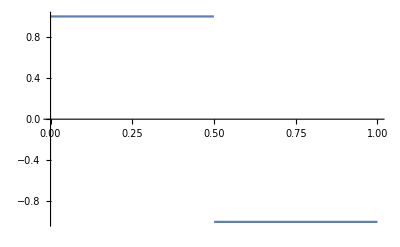

```mathematica
$Assumptions=Subscript[τ, F]>0 && Subscript[τ, χ]>0 && vc>0 && vf>0 && Subscript[τ, i]>0 && Subscript[τ, s]>0 && db>0 && h≥0&& h≤1;
rulof1={Subscript[τ, i]->1,Subscript[τ, s]->1,Subscript[τ, χ]->1,Subscript[τ, F]->1,vf->1,vc->1,db->1};
FullSimplify[D[mu1,ρ]]
FullSimplify[D[mu1,c]]
Plot[FullSimplify[Sign[2*D[mu1,ρ]-D[mu1,c]]],{h,0,1}]
```

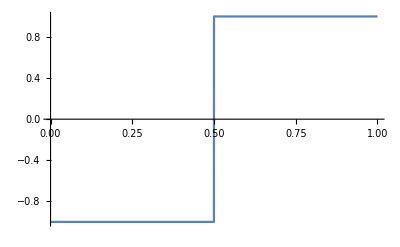

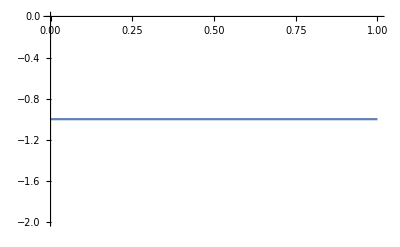

```mathematica
Plot[Sign[D[cstar-bstar,Subscript[ϵ, C]]/.rulof1],{h,0,1}]
Plot[Sign[D[mustar,Subscript[ϵ, C]]/.rulof1],{h,0,1}]
```

```mathematica
Plot[Sign[D[cstar-bstar,Subscript[ϵ, C]]],{h,0,1}]
```

-Graphics-

```mathematica
FullSimplify[Sign[FullSimplify[D[D[cstar-bstar,Subscript[ϵ, C]],Subscript[τ, i]]]]]
```

(Sign[-1+h] Sign[h^3 τ_F^2+(-1+h) h (-1+2 h) vf τ_F τ_s+(-1+h)^3 vf^2 τ_s^2])/(Sign[(-1+h)^2 vf τ_i τ_s+τ_F (h^2 τ_i+2 vc τ_s)]^2)

```mathematica
Flatten[FullSimplify[solge1]/.Rule->Equal]
```

{μ==(m τ_i (τ_F+vf τ_s)+(vf (db+ϵ_F) τ_i+τ_F (db vc-vc ϵ_C+ρ τ_i)+vc vf (db-ϵ_C) τ_s) τ_χ)/(τ_i (τ_F+vf τ_s)+db (vf τ_i+2 vc (τ_F+vf τ_s)) τ_χ),h==(τ_s ((db vf-db m vf+ρ τ_F) τ_i+db vc (vf (db+ϵ_C)+2 ρ τ_F) τ_χ)-ϵ_F (db vf τ_i τ_χ+τ_F (τ_i+2 db vc τ_χ)))/(-db (-1+m) τ_i (τ_F+vf τ_s)+db (-vf ϵ_F τ_i+τ_F (vc (db+ϵ_C)-ρ τ_i)+vc vf (db+ϵ_C) τ_s) τ_χ),b==((db (-1+m) vf-vf ϵ_F-ρ τ_F) τ_i-db vc (vf (db+ϵ_C+2 ϵ_F)+2 ρ τ_F) τ_χ)/(τ_i (τ_F+vf τ_s)+db (vf τ_i+2 vc (τ_F+vf τ_s)) τ_χ),c==-(vc (db (-1+2 m)+ϵ_C) (τ_F+vf τ_s)+db vc (vf (db+ϵ_C+2 ϵ_F)+2 ρ τ_F) τ_χ)/(τ_i (τ_F+vf τ_s)+db (vf τ_i+2 vc (τ_F+vf τ_s)) τ_χ)}

```mathematica
Expand[mustar/Λ]
```

m τ_F τ_i+m vf τ_i τ_s+db vc τ_F τ_χ-vc ϵ_C τ_F τ_χ+db vf τ_i τ_χ+vf ϵ_F τ_i τ_χ+ρ τ_F τ_i τ_χ+db vc vf τ_s τ_χ-vc vf ϵ_C τ_s τ_χ

```mathematica
FullSimplify[bstar/ Λ]
```

(db (-1+m) vf-vf ϵ_F-ρ τ_F) τ_i-db vc (vf (db+ϵ_C+2 ϵ_F)+2 ρ τ_F) τ_χ

```mathematica
FullSimplify[cstar/Λ]
```

-vc (db (-1+2 m)+ϵ_C) (τ_F+vf τ_s)-db vc (vf (db+ϵ_C+2 ϵ_F)+2 ρ τ_F) τ_χ

```mathematica
FullSimplify[cstar/Λ-bstar/Λ ]
```

(-db (-1+m) vf+vf ϵ_F+ρ τ_F) τ_i-vc (db (-1+2 m)+ϵ_C) (τ_F+vf τ_s)

```mathematica
rul1={Subscript[τ, i]->1,Subscript[τ, s]->1,Subscript[τ, χ]->1,Subscript[τ, F]->1,ρ->0,vf->1,vc->1,Subscript[ϵ, C]->-.0,Subscript[ϵ, F]->0,m->.5,db->1};
solge1/.rul1
(*Plot[solge1[[1]][[1]][[2]]/.rul1,{db,-5,5}]*)
```

{{μ→0.571429,h→0.5,b→-0.214286,c→-0.142857}}

```mathematica
.10
```

```mathematica
cpec=FullSimplify[D[cstar,Subscript[ϵ, C]]]
bpec=FullSimplify[D[bstar,Subscript[ϵ, C]]]
mupec=FullSimplify[D[mustar,Subscript[ϵ, C]]]
misalign=cstar-bstar;
```

-(vc (τ_F+vf (τ_s+db τ_χ)))/(τ_i (τ_F+vf τ_s)+db (vf τ_i+2 vc (τ_F+vf τ_s)) τ_χ)

-(db vc vf τ_χ)/(τ_i (τ_F+vf τ_s)+db (vf τ_i+2 vc (τ_F+vf τ_s)) τ_χ)

-(vc (τ_F+vf τ_s) τ_χ)/(τ_i (τ_F+vf τ_s)+db (vf τ_i+2 vc (τ_F+vf τ_s)) τ_χ)

```mathematica
FullSimplify[mupec==Subscript[τ, χ](cpec-bpec)]
```

True

```mathematica
FullSimplify[cstar/Λ-bstar/Λ]
FullSimplify[(mustar-m)/Subscript[τ, χ]/Λ]
```

(-db (-1+m) vf+vf ϵ_F+ρ τ_F) τ_i-vc (db (-1+2 m)+ϵ_C) (τ_F+vf τ_s)

vf (db-db m+ϵ_F) τ_i+τ_F (db vc-2 db m vc-vc ϵ_C+ρ τ_i)+vc vf (db-2 db m-ϵ_C) τ_s

```mathematica
FullSimplify[cstar-bstar]==FullSimplify[(mustar-m)/Subscript[τ, χ]]
```

True

```mathematica
.10
```

```mathematica
misalignnum=FullSimplify[(mustar-m)/(Subscript[τ, χ] Λ)]
Simplify[(mustar-m)/(Subscript[τ, χ] Λ)]
```

vf (db-db m+ϵ_F) τ_i+τ_F (db vc-2 db m vc-vc ϵ_C+ρ τ_i)+vc vf (db-2 db m-ϵ_C) τ_s

τ_F (db vc-2 db m vc-vc ϵ_C+ρ τ_i)+vf ((db-db m+ϵ_F) τ_i+vc (db-2 db m-ϵ_C) τ_s)

```mathematica
Collect[FullSimplify[(mustar-m)/(Subscript[τ, χ] Λ)],{Subscript[τ, i],Subscript[τ, F],Subscript[τ, s]}]
```

(db vc-2 db m vc-vc ϵ_C) τ_F+(vf (db-db m+ϵ_F)+ρ τ_F) τ_i+vc vf (db-2 db m-ϵ_C) τ_s

```mathematica
FullSimplify[D[misalign,Subscript[ϵ, C]]/Λ]
```

-vc (τ_F+vf τ_s)

```mathematica
FullSimplify[D[mustar,Subscript[ϵ, C]]/Λ]
```

-vc (τ_F+vf τ_s) τ_χ

```mathematica
FullSimplify[D[misalign,Subscript[ϵ, F]]/Λ]
```

vf τ_i

Exogenous h = 1, have concentration risk

```mathematica
ClearAll;
Credit;
crdeq=c==vc/Subscript[τ, i]((-2 μ+1) db -Subscript[ϵ, C]);
FX Swap;
fxeq=b==-(db (1-μ) h+Subscript[ϵ, F])/Subscript[τ, s];
Firm;
firmobj=(1-μ) (ye+h (-b-ρ))+μ yu+1/(2 Subscript[τ, χ])(μ-m)^2+1/(2 Subscript[τ, F])db (1-μ)^2 (1-h)^2 vf/.{ye->c+ρ+yu};
feq=FullSimplify[Solve[D[firmobj,μ]==0,μ][[1]][[1]]/.{h->1}]/.Rule->Equal
(*heq=Solve[D[firmobj,h]==0,h][[1]][[1]]/.Rule->Equal*)
$Assumptions=Subscript[τ, F]>0 && Subscript[τ, χ]>0 && vc>0 && vf>0 && Subscript[τ, i]>0 && Subscript[τ, s]>0 && db>0;
solge1=FullSimplify[Solve[{feq,fxeq,crdeq}/.{h->1},{μ,b,c}]]
```

μ==m+(-b+c) τ_χ

{{μ→(vc (db-ϵ_C) τ_s τ_χ+τ_i (m τ_s+(db+ϵ_F) τ_χ))/(τ_i τ_s+db (τ_i+2 vc τ_s) τ_χ),b→((db (-1+m)-ϵ_F) τ_i-db vc (db+ϵ_C+2 ϵ_F) τ_χ)/(τ_i τ_s+db (τ_i+2 vc τ_s) τ_χ),c→-(vc ((db (-1+2 m)+ϵ_C) τ_s+db (db+ϵ_C+2 ϵ_F) τ_χ))/(τ_i τ_s+db (τ_i+2 vc τ_s) τ_χ)}}